# Carnival Corporation Modeling

## Megan Mou, Jonathan Xu, Andrew Zhen, Daniel Wei

## Data Source

```mathematica
data = CompanyData["CarnivalCorporation::3jd9t", "Dataset"]
```

```mathematica
carnivalExpenses = CompanyData["CarnivalCorporation::3jd9t", "TotalExpenses"];
```

```mathematica
carnivalRevenue = CompanyData["CarnivalCorporation::3jd9t", "TotalRevenue"];
```

```mathematica
royalExpenses = CompanyData["RoyalCaribbeanCruises::npc7r", "TotalExpenses"];
```

```mathematica
royalRevenue = CompanyData["RoyalCaribbeanCruises::npc7r", "TotalRevenue"];
```

```mathematica
norwegianExpenses = CompanyData["NorwegianCruiseLineHoldings::5jq73", "TotalExpenses"];
```

```mathematica
norwegianRevenue = CompanyData["NorwegianCruiseLineHoldings::5jq73", "TotalRevenue"];
```

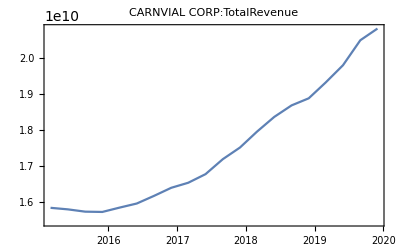

Set::write: Tag Slot in #plotCarnivalexp is Protected.

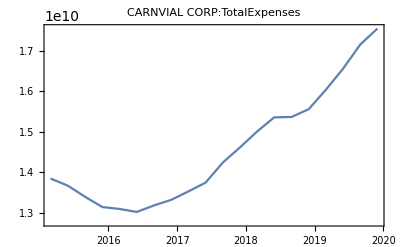

Set::write: Tag Slot in #plotCarnivalasset is Protected.

```mathematica
plotCompanyFundamentalDataOneSeries[symbol_,startDate_,endDate_,id_]:=Module[{mycompany,mycompanydata},mycompany=EntityValue[Interpreter["Company"][symbol],"Company"];
mycompanydata=EntityValue[mycompany,Dated[id,Interval[{DateObject[startDate],DateObject[endDate]}]]];
DateListPlot[mycompanydata,PlotLabel->symbol<>":"<>id,PlotTheme->"Detailed"]]
plotCarnivalrev = GraphicsColumn[{plotCompanyFundamentalDataOneSeries["CARNVIAL CORP",{2015,1,1},{2020,1,1},"TotalRevenue"]}]
#plotCarnivalexp = GraphicsColumn[{plotCompanyFundamentalDataOneSeries["CARNVIAL CORP",{2015,1,1},{2020,1,1},"TotalExpenses"]}]
#plotCarnivalasset = GraphicsColumn[{plotCompanyFundamentalDataOneSeries["CARNVIAL CORP",{2015,1,1},{2020,1,1},"TotalAssets"]}];
```

```mathematica
FinancialData["CARNIVAL CORP","Revenue",{{2000,1,1},{2000,4,1}}]
```

FinancialData[CARNIVAL CORP,Revenue,{{2000,1,1},{2000,4,1}}]